```mathematica
2-2
```

0

```mathematica
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
```

# Quantum Vortices in a Square Well

Nicholas Wheeler
Reed College Physics
2 May 2008

### Introduction

I was asked recently by the acting editor of AJP to referee a paper "Quantum-mechanical phase vortices in the two-dimensional infinite square well" by Meredith A. Mahoney, David M. Paganin & Helen M. L. Faulkner. I made heavy use of Mathematica in preparing and illustrating my report (which survives as a couple of pdf files), but the notebooks generated by that effort were considered to be mere worksheets, and were left in a very disorganized state. I was motivated by MPF to undertake the work recorded in "Quantum vortices in a circular well," which I had imagined would be relatively more interesting/instructive, but were discovered to be less so. So I have come belatedly to value the MPF work for its computational tractability and the vividness of the results to which it leads, and am motivated to undertake this more careful account of my own work in this subject area.

### Some preliminary remarks of a general nature

Let  Ψ[x, y] be written in polar form

```mathematica
Ψ=R Exp[ⅈ/ℏ S];
Ψstar=R Exp[-ⅈ/ℏ S];
```

with

```mathematica
R=r[x,y,t];
S=s[x,y,t];
```

Supposing Ψ[x, y] to be a solution of the free-particle Schrödinger equation, we construct

```mathematica
Schrödinger=Exp[-ⅈ/ℏ S](-ℏ^2/(2m)(D[Ψ,{x,2}]+D[Ψ,{y,2}])-ⅈ ℏ D[Ψ,t])//Expand
```

-ⅈ ℏ r^(0,0,1)[x,y,t]+r[x,y,t] s^(0,0,1)[x,y,t]-(ⅈ ℏ r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t] (s^(0,1,0)[x,y,t])^2)/(2 m)-(ℏ^2 r^(0,2,0)[x,y,t])/(2 m)-(ⅈ ℏ r[x,y,t] s^(0,2,0)[x,y,t])/(2 m)-(ⅈ ℏ r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t] (s^(1,0,0)[x,y,t])^2)/(2 m)-(ℏ^2 r^(2,0,0)[x,y,t])/(2 m)-(ⅈ ℏ r[x,y,t] s^(2,0,0)[x,y,t])/(2 m)

from which we extract and massage the real and imaginary parts (which must vanish separately):

```mathematica
(CompConj[Schrödinger]+Schrödinger)/(2  r[x,y,t])//Expand
(CompConj[Schrödinger]-Schrödinger)/(2 ℏ ⅈ)//Expand
```

s^(0,0,1)[x,y,t]+((s^(0,1,0)[x,y,t])^2)/(2 m)-(ℏ^2 r^(0,2,0)[x,y,t])/(2 m r[x,y,t])+((s^(1,0,0)[x,y,t])^2)/(2 m)-(ℏ^2 r^(2,0,0)[x,y,t])/(2 m r[x,y,t])

r^(0,0,1)[x,y,t]+(r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t] s^(0,2,0)[x,y,t])/(2 m)+(r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t] s^(2,0,0)[x,y,t])/(2 m)

The first equation can be written

s^(0,0,1)[x,y,t]+((s^(0,1,0)[x,y,t])^2)/(2 m)+((s^(1,0,0)[x,y,t])^2)/(2 m)=(ℏ^2( r^(2,0,0)[x,y,t]+r^(0,2,0)[x,y,t]))/(2 m r[x,y,t])

where in classical theory the expression on the left would vanish by appeal to Hamilton-Jacobi theory. The second equation finds employment at the end of the next paragraph:

The probability density is given then by

```mathematica
Ψstar Ψ
```

r[x,y,t]^2

and the probability current by

```mathematica
Subscript[J, x]=ℏ/(2m ⅈ)(Ψstar D[Ψ,x]-Ψ D[Ψstar,x])//Simplify
Subscript[J, y]=ℏ/(2m ⅈ)(Ψstar D[Ψ,y]-Ψ D[Ψstar,y])//Simplify
```

(r[x,y,t]^2 s^(1,0,0)[x,y,t])/m

(r[x,y,t]^2 s^(0,1,0)[x,y,t])/m

The continuity equation that provides a local account of probability conservation lends interest to a construction

```mathematica
D[r[x,y,t]^2,t]+D[(r[x,y,t]^2 Derivative[1,0,0][s][x,y,t])/m,x]+D[(r[x,y,t]^2 Derivative[0,1,0][s][x,y,t])/m,y]//Expand
```

2 r[x,y,t] r^(0,0,1)[x,y,t]+(2 r[x,y,t] r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t]^2 s^(0,2,0)[x,y,t])/m+(2 r[x,y,t] r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t]^2 s^(2,0,0)[x,y,t])/m

that after only a little massaging leads to a construction that has already been shown to vanish;

```mathematica
%/r[x,y,t]//Expand
```

2 r^(0,0,1)[x,y,t]+(2 r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t] s^(0,2,0)[x,y,t])/m+(2 r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t] s^(2,0,0)[x,y,t])/m

```mathematica
%==(CompConj[Schrödinger]-Schrödinger)/(2 ℏ ⅈ)//Expand
```

2 r^(0,0,1)[x,y,t]+(2 r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t] s^(0,2,0)[x,y,t])/m+(2 r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t] s^(2,0,0)[x,y,t])/m==r^(0,0,1)[x,y,t]+(r^(0,1,0)[x,y,t] s^(0,1,0)[x,y,t])/m+(r[x,y,t] s^(0,2,0)[x,y,t])/(2 m)+(r^(1,0,0)[x,y,t] s^(1,0,0)[x,y,t])/m+(r[x,y,t] s^(2,0,0)[x,y,t])/(2 m)

The vector-valued construction

(probability current)/(probability density)

has the physical dimension of a "velocity." It was shown above that

quantum mechanical velocity field ≡ (probability currrent)/(probability density)=1/m Grad[S]

Exists except

The velocity field

(V_x[x,y,t]
V_y[x,y,t])=(J_x[x,y,t]
J_y[x,y,t])/P[x,y,t]=1/m Grad[S]

exists except where the probability density P[x,y,z,t] vanishes (which is to say: where Ψ[x,y,z,t] vanishes), and might exist even at such points if  J[x,y,z,t] happened also to vanish in just the right way. At those points the phase must be undifferentiable (discontinuous).

In fluid dynamics (see §1.2—"Rotation and Vorticity"—pages 19-31 in A. J. Chorin & J. E. Marsden, A Mathematical Introduction to Fluid Mechanics (2nd edition, 1990)) the vector-valued field produced by constructing the curl of a velocity field is called the "vorticity":

Ω=Curl[V]

For the "quantum mechanical probability fluid" one has

Ω=1/m Curl[ Grad[S]]=0

except at singular points (points where phase discontinuities cause  Grad[S]  to be undefined).

### Quantum vorticity of a toy model

Let us agree, now and hencforth, to adopt units in which

2m = ℏ = 1

The 2-dimensional free-particle Schrödinger equation then reads

-((∂_x)^2+(∂_y)^2)ψ=ⅈ ∂_t ψ

I have need now of this

A seldom remarked point: Let

Ψ[x,y,t,α,β]

be a solution of the Schrödinger equation that depends upon certain parameters {α, β, ...}. Then (by linearity)

Ψ_mn[x,y,t,α,β]=(∂_α)^m(∂_β)^n Ψ[x,y,t,α,β]

is also a solution. So are all real/complex linear combinations of such functions. Note, however, that functions produced in this way will, in general, not mimic the boundary conditions satisfied by the mother function Ψ. Nor will they, in general, be normalized.

Look, for example, to the function

```mathematica
Ψ=Exp[ⅈ(α x+β y-(α^2+β^2) t)]
```

ⅇ^(ⅈ (x α+y β-t (α^2+β^2)))

which clearly does satisfy the free-particle Schrödinger equation:

```mathematica
-D[Ψ,{x,2}]-D[Ψ,{y,2}]-ⅈ D[Ψ,{t,1}]//Simplify
```

0

Construct

```mathematica
Subscript[Ψ, 11]=-ⅈ D[Ψ,{α,1}]+ D[Ψ,{β,1}]//Simplify
```

ⅇ^(ⅈ (x α+y β-t (α^2+β^2))) (x+ⅈ (y+2 ⅈ t α-2 t β))

which we (by the "seldom remarked point") know, but will anyway demonstrate, satisfies the Schrödinger equation:

```mathematica
-D[Subscript[Ψ, 11],{x,2}]-D[Subscript[Ψ, 11],{y,2}]-ⅈ D[Subscript[Ψ, 11],{t,1}]//Simplify
```

0

From

```mathematica
Subscript[Ψ, 11] CompConj[Subscript[Ψ, 11]]//ComplexExpand
```

x^2+y^2-4 t x α+4 t^2 α^2-4 t y β+4 t^2 β^2

we are led to define the density

```mathematica
P[x_,y_,t_,α_,β_]:=x^2+y^2-4 t x α+4 t^2 α^2-4 t y β+4 t^2 β^2
```

which, though everywhere non-negative, is not normalized, so cannot be interpreted as "probability density." Introducing the associated current (which is not "probability current")

```mathematica
-ⅈ(CompConj[Subscript[Ψ, 11]] D[Subscript[Ψ, 11],x]-Subscript[Ψ, 11] D[ CompConj[Subscript[Ψ, 11]],x])//Expand
-ⅈ(CompConj[Subscript[Ψ, 11]] D[Subscript[Ψ, 11],y]-Subscript[Ψ, 11] D[ CompConj[Subscript[Ψ, 11]],y])//Expand
```

-2 y+2 x^2 α+2 y^2 α-8 t x α^2+8 t^2 α^3+4 t β-8 t y α β+8 t^2 α β^2

2 x-4 t α+2 x^2 β+2 y^2 β-8 t x α β+8 t^2 α^2 β-8 t y β^2+8 t^2 β^3

```mathematica
JX[x_,y_,t_,α_,β_]:=-2 y+2 x^2 α+2 y^2 α-8 t x α^2+8 t^2 α^3+4 t β-8 t y α β+8 t^2 α β^2
JY[x_,y_,t_,α_,β_]:=2 x-4 t α+2 x^2 β+2 y^2 β-8 t x α β+8 t^2 α^2 β-8 t y β^2+8 t^2 β^3
```

we confirm that we do have the anticipated local conservation law (continuity equation)

```mathematica
D[P[x,y,t,α,β],t]+D[JX[x,y,t,α,β],x]+D[JY[x,y,t,α,β],y]//Simplify
```

0

```mathematica
Needs["VectorFieldPlots`"]
```

```mathematica
Manipulate[Plot3D[P[x,y,t,α,β],{x,-1,1},{y,-1,1}, PlotRange->{0,20}, Ticks->False, PlotLabel->"Probability Density", LabelStyle->Directive[Bold, Red]],{t,0,1},{α,-1,1},{β,-1,1}]
Manipulate[VectorFieldPlot[{JX[x,y,t,α,β],JY[x,y,t,α,β]},{x,-1,1},{y,-1,1}, PlotLabel->"Probability Current", LabelStyle->Directive[Bold, Red]],{t,0,1},{α,-1,1},{β,-1,1}]
```

The figure reveals a moving swirl when α and β are assigned non-zero values.

The probability density vanishes if and only the wave function itself vanishes, which requires that its real and imaginary parts both vanish. From

```mathematica
Subscript[Ψ, 11]
```

ⅇ^(ⅈ (x α+y β-t (α^2+β^2))) (x+ⅈ (y+2 ⅈ t α-2 t β))

we learn that the probability density vanishes (and the velocity field becomes singular) at a point  {x,y} that moves linearly

```mathematica
x-2α t=0
y-2β t=0
```

0

0

```mathematica
P[x,y,t,α,β]/.{x->2α t, y->2β t}
```

0

The velocity field is defined

```mathematica
VX[x_,y_,t_ ,α_,β_]:=JX[x,y,t,α,β]/P[x,y,t,α,β]
VY[x_,y_,t_ ,α_,β_]:=JY[x,y,t,α,β]/P[x,y,t,α,β]
```

```mathematica
VX[x,y,t,α,β]
```

(-2 y+2 x^2 α+2 y^2 α-8 t x α^2+8 t^2 α^3+4 t β-8 t y α β+8 t^2 α β^2)/(x^2+y^2-4 t x α+4 t^2 α^2-4 t y β+4 t^2 β^2)

but to humor Mathematica—to keep her from complaining

```mathematica
VX[x,y,t,α,β]/.{x->2α t, y->2β t}
```

Indeterminate

—we adopt this modified definition:

```mathematica
Clear[α]
```

```mathematica
VVX[x,y,t,α,β]
```

VVX[x,y,t,α,β]

```mathematica
VVX[x_,y_,t_ ,α_,β_]:=JX[x,y,t,α,β]/(P[x,y,t,α,β]+0.00000001)
VVY[x_,y_,t_ ,α_,β_]:=JY[x,y,t,α,β]/(P[x,y,t,α,β]+0.00000001)
```

```mathematica
Manipulate[VectorFieldPlot[{VVX[x,y,t,α,β],VVY[x,y,t,α,β]},{x,-1,1},{y,-1,1}, PlotLabel->"Velocity Field", LabelStyle->Directive[Bold, Red]],{t,0,1},{α,-1,1},{β,-1,1}]
```

The vorticity (curl of the velocity field) is in 2-dimensional theory a pseudoscalar field, known from preceding remarks to vanish

```mathematica
D[VY[x,y,t,α,β],x]- D[VX[x,y,t,α,β],y]//Simplify
```

0

except at the singular point. To expose the singularity to grapic scrutiny, we proceed from

```mathematica
D[VVY[x,y,t,α,β],x]- D[VVX[x,y,t,α,β],y]//Simplify
```

(4.×10^-8-4.×10^-8 y α+4.×10^-8 x β)/((1.×10^-8+x^2+y^2-4. t x α+4. t^2 α^2-4. t y β+4. t^2 β^2)^2)

to the definition

```mathematica
ΩΩ[x_,y_,t_ ,α_,β_]:=(4.*^-8-4.*^-8 y α+4.*^-8 x β)/((1.*^-8+x^2+y^2-4. t x α+4. t^2 α^2-4. t y β+4. t^2 β^2)^2)
```

This function has a large value at the singularity (located at the origin of the {x,y}-plane when t = α = β =0)

```mathematica
ΩΩ[0,0,0,0,0]
```

4.×10^8

but falls to very small values at close-by points

```mathematica
ΩΩ[0.01,0.01,0,0,0]
ΩΩ[0.1,0.1,0,0,0]
```

0.9999

0.0000999999

As previously remarked, we expect the singular point to be a point at which the phase of the wave function

```mathematica
ΨΨ[x_,y_,t_,α_,β_]:=ⅇ^(ⅈ (x α+y β-t (α^2+β^2))) (x+ⅈ (y+2 ⅈ t α-2 t β))
```

becomes undifferentiable. The close relationship between the vorticity and phase singularities is illustrated in the following sequence of paired figures

```mathematica
Plot3D[ΩΩ[x,y,0,0,0],{x,-1,1},{y,-1,1}, PlotRange->{-100,100}, Ticks->False, PlotPoints->100, PlotLabel->"Vorticity", LabelStyle->Directive[Bold, Red]]
Plot3D[
Arg[ΨΨ[x,y,0,0,0]],{x,-1,1},{y,-1,1}, PlotRange->{-π,π}, Ticks->{{},{},{-π,π}}, PlotPoints->100,PlotLabel->Style["Phase Singularity",Bold,Red]]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[ΩΩ[x,y,.25,.25,.25],{x,-1,1},{y,-1,1}, PlotRange->{-100,100}, Ticks->False, PlotPoints->100, PlotLabel->"Vorticity", LabelStyle->Directive[Bold, Red]]
Plot3D[
Arg[ΨΨ[x,y,.25,.25,.25]],{x,-1,1},{y,-1,1}, PlotRange->{-π,π}, PlotPoints->100, Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase Singularity",Bold,Red]]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[ΩΩ[x,y,.5,.5,.5],{x,-1,1},{y,-1,1}, PlotRange->{-100,100}, Ticks->False, PlotPoints->100, PlotLabel->"Vorticity", LabelStyle->Directive[Bold, Red]]
Plot3D[
Arg[ΨΨ[x,y,.5,.5,.5]],{x,-1,1},{y,-1,1}, PlotRange->{-π,π},  PlotPoints->100, Ticks->{{},{},{-π,π}},PlotLabel->Style["Phase Singularity",Bold,Red]]
```

-Graphics3D-

-Graphics3D-

To expose most clearly the anatomy of the phase singularity one can (as MPF advocate) construct the first-order Taylor expansion of  ΨΨ[x,y,t,α,β] about the singular point x = 2 α t, y = 2 β t.

```mathematica
Series[ΨΨ[2α t+dx,2β t+dy,t,α,β],{dx,0,1},{dy,0,1}]
```

(ⅈ ⅇ^(ⅈ t α^2+ⅈ t β^2) dy+O[dy]^2)+(ⅇ^(ⅈ t α^2+ⅈ t β^2)+(-ⅇ^(ⅈ t α^2+ⅈ t β^2) α+ⅈ ⅇ^(ⅈ t α^2+ⅈ t β^2) β) dy+O[dy]^2) dx+O[dx]^2

Use that information to construct the following function, which is "tangent to the wave function at the point where it vanishes"

```mathematica
Clear[ψ]
```

```mathematica
ψ[dx_,dy_,t_,α_,β_]:=ⅇ^(ⅈ t α^2+ⅈ t β^2)(dx+ⅈ dy)
```

and then examine the phase of that relatively simple function:

```mathematica
Plot3D[
Arg[ψ[dx,dy,.5,.5,.5]],{dx,-.1,.1},{dy,-.1,.1}, PlotRange->{-π,π}, PlotPoints->100, Ticks->{{},{},{-π,π}},PlotLabel->Style["Close-up  Detail of the Phase Singularity",Bold,Red]]
```

-Graphics3D-

### Energy eigenfunctions for the one-dimensional square well of infinite depth

We seek normalized solutions of the time-independent Schrödinger equation

-(∂_x)^2 ψ[x]=ℰ  ψ[x]

that conform to the boundary conditions

ψ[0]=ψ[1]=0

We are led to the functions

```mathematica
f1[x_]:=√2 Sin[1π x]
f2[x_]:=√2 Sin[2π x]
f3[x_]:=√2 Sin[3π x]
```

and their higher order relatives.

```mathematica
∫_0^1 f1[x]^2 ⅆx
∫_0^1 f2[x]^2 ⅆx
∫_0^1 f3[x]^2 ⅆx
```

1

1

1

```mathematica
(-D[f1[x],{x,2}])/f1[x]
(-D[f2[x],{x,2}])/f2[x]
(-D[f3[x],{x,2}])/f3[x]
```

π^2

4 π^2

9 π^2

Generally, ℰ_n=n^2 π^2 so the buzzing eigenfunctions (solutions of the time-dependent Schrödinger equation) are

```mathematica
F1[x_,t_]:=f1[x]Exp[-ⅈ 1^2 π^2 t]
F2[x_,t_]:=f2[x]Exp[-ⅈ 2^2 π^2 t]
F3[x_,t_]:=f3[x]Exp[-ⅈ 3^2 π^2 t]
```

```mathematica
-D[F1[x,t],{x,2}]-ⅈ D[F1[x,t],t]
-D[F2[x,t],{x,2}]-ⅈ D[F2[x,t],t]
-D[F3[x,t],{x,2}]-ⅈ D[F3[x,t],t]
```

0

0

0

### Energy eigenfunctions for the two-dimensional square well of infinite depth

The system separates into two copies of the system just studied, so we are led immediately to the buzzing normalized eigenfunctions

```mathematica
F11[x_,y_,t_]:=f1[x]f1[y]Exp[-ⅈ π^2(1^2+1^2)t]
F12[x_,y_,t_]:=f1[x]f2[y]Exp[-ⅈ π^2(1^2+2^2)t]
F13[x_,y_,t_]:=f1[x]f3[y]Exp[-ⅈ π^2(1^2+3^2)t]
F21[x_,y_,t_]:=f2[x]f1[y]Exp[-ⅈ π^2(2^2+1^2)t]
F22[x_,y_,t_]:=f2[x]f2[y]Exp[-ⅈ π^2(2^2+2^2)t]
F23[x_,y_,t_]:=f2[x]f3[y]Exp[-ⅈ π^2(2^2+3^2)t]
F31[x_,y_,t_]:=f3[x]f1[y]Exp[-ⅈ π^2(3^2+1^2)t]
F32[x_,y_,t_]:=f3[x]f2[y]Exp[-ⅈ π^2(3^2+2^2)t]
F33[x_,y_,t_]:=f3[x]f3[y]Exp[-ⅈ π^2(3^2+3^2)t]
```

These functions are obviously/demonstrably normalized

```mathematica
∫_0^1 (∫_0^1 F12[x,y,t]CompConj[F12[x,y,t]]ⅆx)ⅆy
```

1

and obviously/demonstrably satisfy the Schrödinger equation:

```mathematica
-D[F12[x,y,t],{x,2}]-D[F12[x,y,t],{y,2}]==ⅈ D[F12[x,y,t],t]
```

True

Their probability densities are (of course) time-independent

```mathematica
Prob1212[x_,y_,t_]:=F12[x,y,t]CompConj[F12[x,y,t]]
```

```mathematica
Prob1212[x,y,t]
```

4 Sin[π x]^2 Sin[2 π y]^2

```mathematica
Plot3D[4 Sin[π x]^2 Sin[2 π y]^2,{x,0,1},{y,0,1},Ticks->False,PlotLabel->"Static Probability Density of a Buzzing Eigenfunction", LabelStyle->Directive[Bold, Red]]
```

-Graphics3D-

and the associated probability currents vanish:

```mathematica
-ⅈ(CompConj[F12[x,y,t]]D[F12[x,y,t],x]-F12[x,y,t]D[CompConj[F12[x,y,t]],x])
-ⅈ(CompConj[F12[x,y,t]]D[F12[x,y,t],y]-F12[x,y,t]D[CompConj[F12[x,y,t]],y])
```

0

0

To produce motion—which in quantum mechanics is an interference effect—one must take such functions in (normalized) linear combination. In the simplest instance we have constructs of the form

```mathematica
Clear[Ψ,μ,ϕ]
```

```mathematica
Ψ[x_,y_,t_,μ_,ϕ_]:=Cos[μ]F21[x,y,t]+ⅇ^(ⅈ ϕ)Sin[μ]F12[x,y,t]
```

```mathematica
Ψ[x,y,t,μ,ϕ]
```

2 ⅇ^(-5 ⅈ π^2 t) Cos[μ] Sin[2 π x] Sin[π y]+2 ⅇ^(-5 ⅈ π^2 t+ⅈ ϕ) Sin[π x] Sin[2 π y] Sin[μ]

where μ is a "mixing angle" and ϕ a "relative phase" factor. For no better reason than to achieve agreement with MPF I set

FIRST EXAMPLE

For no better reason than to achieve agreement with MPF, I set

```mathematica
μ=ArcCos[2/3]
ϕ=ArcTan[2]
```

ArcCos[2/3]

ArcTan[2]

```mathematica
Cos[μ]
ⅇ^(ⅈ ϕ)Sin[μ]//ComplexExpand
```

2/3

1/3+(2 ⅈ)/3

```mathematica
Ψ=2/3 F21[x,y,t]+(1+2ⅈ)/3 F12[x,y,t]
```

4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y]

```mathematica
ψ=Ψ/.t->0
```

4/3 Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) Sin[π x] Sin[2 π y]

```mathematica
ψstar=4/3 Sin[2 π x] Sin[π y]+(2/3-(4 ⅈ)/3) Sin[π x] Sin[2 π y]
```

4/3 Sin[2 π x] Sin[π y]+(2/3-(4 ⅈ)/3) Sin[π x] Sin[2 π y]

```mathematica
ψstar ψ//ComplexExpand
```

16/9 Sin[2 π x]^2 Sin[π y]^2+16/9 Sin[π x] Sin[2 π x] Sin[π y] Sin[2 π y]+20/9 Sin[π x]^2 Sin[2 π y]^2

```mathematica
P[x_,y_]:=16/9 Sin[2 π x]^2 Sin[π y]^2+16/9 Sin[π x] Sin[2 π x] Sin[π y] Sin[2 π y]+20/9 Sin[π x]^2 Sin[2 π y]^2
```

```mathematica
∫_0^1 (∫_0^1 P[x,y]ⅆx)ⅆy
```

1

```mathematica
Plot3D[P[x,y],{x,0,1},{y,0,1},Ticks->False,PlotLabel->"Initial Probability Density: Example 1", LabelStyle->Directive[Bold, Red]]
```

-Graphics3D-

It is evident from the figure, but I now verify, that the initial probability density vanishes at the middle of the box:

```mathematica
P[1/2,1/2]
```

0

```mathematica
-ⅈ(ψstar D[ψ,x]-ψ D[ψstar,x])//ComplexExpand
-ⅈ(ψstar D[ψ,y]-ψ D[ψstar,y])//ComplexExpand
```

-64/9 π Cos[2 π x] Sin[π x] Sin[π y] Sin[2 π y]+32/9 π Cos[π x] Sin[2 π x] Sin[π y] Sin[2 π y]

64/9 π Cos[2 π y] Sin[π x] Sin[2 π x] Sin[π y]-32/9 π Cos[π y] Sin[π x] Sin[2 π x] Sin[2 π y]

```mathematica
JX[x_,y_]:=-64/9 π Cos[2 π x] Sin[π x] Sin[π y] Sin[2 π y]+32/9 π Cos[π x] Sin[2 π x] Sin[π y] Sin[2 π y]
JY[x_,y_]:=64/9 π Cos[2 π y] Sin[π x] Sin[2 π x] Sin[π y]-32/9 π Cos[π y] Sin[π x] Sin[2 π x] Sin[2 π y]
```

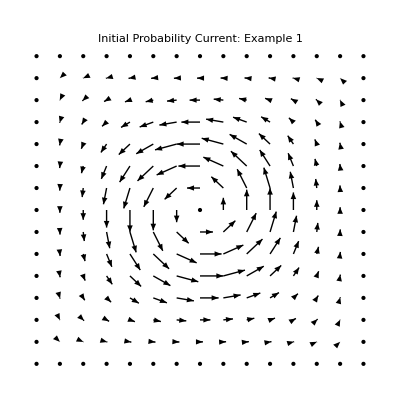

```mathematica
VectorFieldPlot[{JX[x,y],JY[x,y]},{x,0,1},{y,0,1},PlotLabel->"Initial Probability Current: Example 1", LabelStyle->Directive[Bold, Red]]
```

```mathematica
JX[x,y]/(P[x,y]+0.000001)
```

(-64/9 π Cos[2 π x] Sin[π x] Sin[π y] Sin[2 π y]+32/9 π Cos[π x] Sin[2 π x] Sin[π y] Sin[2 π y])/(1.×10^-6+16/9 Sin[2 π x]^2 Sin[π y]^2+16/9 Sin[π x] Sin[2 π x] Sin[π y] Sin[2 π y]+20/9 Sin[π x]^2 Sin[2 π y]^2)

```mathematica
VVX[x_,y_]:=JX[x,y]/(P[x,y]+0.000001)
VVY[x_,y_]:=JY[x,y]/(P[x,y]+0.000001)
```

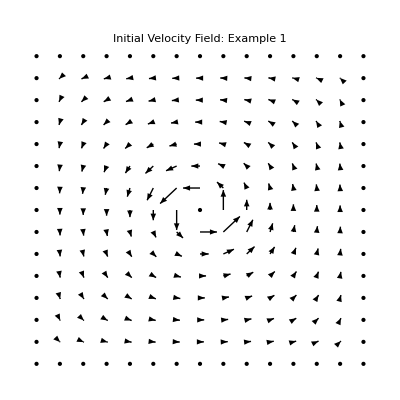

```mathematica
VectorFieldPlot[{VVX[x,y],VVY[x,y]},{x,0,1},{y,0,1},PlotLabel->"Initial Velocity Field: Example 1", LabelStyle->Directive[Bold, Red]]
```

```mathematica
D[VVY[x,y],x]-D[VVX[x,y],y]//Simplify
```

(0.000280735 Cos[2 π x] Cos[2 π y] Sin[π x] Sin[π y]-0.0000701839 Cos[π x] Cos[π y] Sin[2 π x] Sin[2 π y])/(1.×10^-6+1.77778 Sin[2 π x]^2 Sin[π y]^2+1.77778 Sin[π x] Sin[2 π x] Sin[π y] Sin[2 π y]+2.22222 Sin[π x]^2 Sin[2 π y]^2)^2

```mathematica
Ω[x_,y_]:=(0.00028073541407543063 Cos[2 π x] Cos[2 π y] Sin[π x] Sin[π y]-0.00007018385351885766 Cos[π x] Cos[π y] Sin[2 π x] Sin[2 π y])/(1.*^-6+1.7777777777777777 Sin[2 π x]^2 Sin[π y]^2+1.7777777777777777 Sin[π x] Sin[2 π x] Sin[π y] Sin[2 π y]+2.2222222222222223 Sin[π x]^2 Sin[2 π y]^2)^2
```

```mathematica
Plot3D[Ω[x,y],{x,0,1},{y,0,1}, PlotRange->{0,10},PlotPoints->{100}, Ticks->False,PlotLabel->"Initial Vorticity: Example 1", LabelStyle->Directive[Bold, Red]]
```

-Graphics3D-

```mathematica
Plot3D[Arg[4/3 Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) Sin[π x] Sin[2 π y]],{x,0,1},{y,0,1}, PlotRange->{-π,π},PlotPoints->{100},  Ticks->{{},{},{-π,π}},PlotLabel->Style["Initial Phase: Example 1",Bold,Red]]
```

-Graphics3D-

SECOND EXAMPLE

Here, following again in the steps of MPF, I use

```mathematica
Cos[π/4]
ⅇ^(ⅈ π/2)Sin[π/4]
```

1/(√2)

ⅈ/(√2)

to assemble

```mathematica
ψ2[x_,y_,t_]:=1/(√2)F31[x,y,t]+ⅈ/(√2)F13[x,y,t]
```

```mathematica
ψ2[x,y,t]
```

√2 ⅇ^(-10 ⅈ π^2 t) Sin[3 π x] Sin[π y]+ⅈ √2 ⅇ^(-10 ⅈ π^2 t) Sin[π x] Sin[3 π y]

```mathematica
ψ2star[x_,y_,t_]:=√2 ⅇ^(+10 ⅈ π^2 t) Sin[3 π x] Sin[π y]-ⅈ √2 ⅇ^(+10 ⅈ π^2 t) Sin[π x] Sin[3 π y]
```

Proceeding now through the familiar sequence of constructions…

```mathematica
ψ2star[x,y,0]ψ2[x,y,0]//ComplexExpand
```

2 Sin[3 π x]^2 Sin[π y]^2+2 Sin[π x]^2 Sin[3 π y]^2

```mathematica
P2[x_,y_]:=2 Sin[3 π x]^2 Sin[π y]^2+2 Sin[π x]^2 Sin[3 π y]^2
```

```mathematica
Plot3D[P2[x,y],{x,0,1},{y,0,1}, Ticks->False,PlotLabel->"Initial Probability Density: Example 2", LabelStyle->Directive[Bold, Red]]
```

-Graphics3D-

```mathematica
-ⅈ(ψ2star[x,y,0] D[ψ2[x,y,0],x]-ψ2[x,y,0] D[ψ2star[x,y,0],x])//ComplexExpand
-ⅈ(ψ2star[x,y,0] D[ψ2[x,y,0],y]-ψ2[x,y,0] D[ψ2star[x,y,0],y])//ComplexExpand
```

-12 π Cos[3 π x] Sin[π x] Sin[π y] Sin[3 π y]+4 π Cos[π x] Sin[3 π x] Sin[π y] Sin[3 π y]

12 π Cos[3 π y] Sin[π x] Sin[3 π x] Sin[π y]-4 π Cos[π y] Sin[π x] Sin[3 π x] Sin[3 π y]

```mathematica
JX2[x_,y_]:=-12 π Cos[3 π x] Sin[π x] Sin[π y] Sin[3 π y]+4 π Cos[π x] Sin[3 π x] Sin[π y] Sin[3 π y]
JY2[x_,y_]:=12 π Cos[3 π y] Sin[π x] Sin[3 π x] Sin[π y]-4 π Cos[π y] Sin[π x] Sin[3 π x] Sin[3 π y]
```

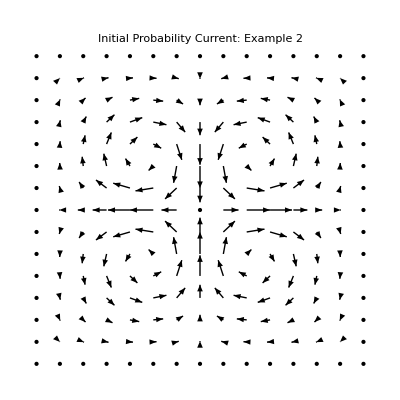

```mathematica
VectorFieldPlot[{JX2[x,y],JY2[x,y]},{x,0,1},{y,0,1},PlotLabel->"Initial Probability Current: Example 2", LabelStyle->Directive[Bold, Red]]
```

```mathematica
VX2[x_,y_]:=JX2[x,y]/(P2[x,y]+0.00000001)
VY2[x_,y_]:=JY2[x,y]/(P2[x,y]+0.00000001)
```

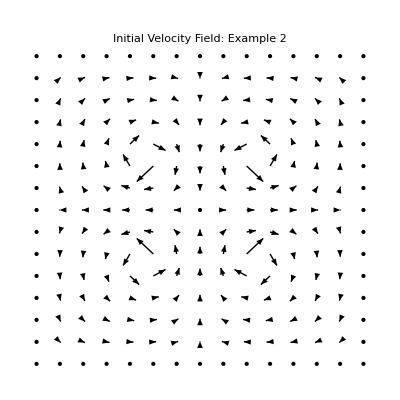

```mathematica
VectorFieldPlot[{VX2[x,y],VY2[x,y]},{x,0,1},{y,0,1},PlotLabel->"Initial Velocity Field: Example 2", LabelStyle->Directive[Bold, Red]]
```

```mathematica
D[VY2[x,y],x]-D[VX2[x,y],y]//Simplify
```

(7.10612×10^-6 Cos[3 π x] Cos[3 π y] Sin[π x] Sin[π y]-7.89568×10^-7 Cos[π x] Cos[π y] Sin[3 π x] Sin[3 π y])/(1.×10^-8+2. Sin[3 π x]^2 Sin[π y]^2+2. Sin[π x]^2 Sin[3 π y]^2)^2

```mathematica
Ω2[x_,y_]:=(7.106115168784338*^-6 Cos[3 π x] Cos[3 π y] Sin[π x] Sin[π y]-7.895683520871487*^-7 Cos[π x] Cos[π y] Sin[3 π x] Sin[3 π y])/(1.*^-8+2. Sin[3 π x]^2 Sin[π y]^2+2. Sin[π x]^2 Sin[3 π y]^2)^2
```

```mathematica
Plot3D[Ω2[x,y],{x,0,1},{y,0,1},PlotPoints->100, PlotRange->{-100,100},Ticks->False,PlotLabel->"Initial Vorticity: Example 2", LabelStyle->Directive[Bold, Red]]
```

-Graphics3D-

```mathematica
Plot3D[Arg[ψ2[x,y,0]],{x,0,1},{y,0,1},Ticks->{{},{},{-π,π}},PlotLabel->Style["Initial Phase: Example 2",Bold,Red]]
```

-Graphics3D-

The singularities are positioned at {1/3,1/3},  {1/3,2/3}, {2/3,1/3}, {2/3,2/3}

Looking here only to the first of those, we have

```mathematica
Series[ψ2[1/3+dx,1/3+dy,t],{dx,0,1},{dy,0,1}]
```

(-3 ⅈ √(3/2) ⅇ^(-10 ⅈ π^2 t) π dy+O[dy]^2)+(-3 (√(3/2) ⅇ^(-10 ⅈ π^2 t) π)-((3+3 ⅈ) ⅇ^(-10 ⅈ π^2 t) π^2 dy)/(√2)+O[dy]^2) dx+O[dx]^2

so in first order

-3 ⅈ √(3/2) ⅇ^(-10 ⅈ π^2 t) π dy-3 (√(3/2) ⅇ^(-10 ⅈ π^2 t) π)dx

```mathematica
LocalPhase[dx_,dy_,t_]:=-3 ⅈ √(3/2) ⅇ^(-10 ⅈ π^2 t) π dy-3 (√(3/2) ⅇ^(-10 ⅈ π^2 t) π)dx
```

```mathematica
Manipulate[Plot3D[Arg[LocalPhase[dx,dy, k/12(2π)/(10 π^2)]],{dx,-1/3,2/3},{dy,-1/3,2/3},Ticks->{{},{},{-π,π}},PlotLabel->Style["Time-dependence of phase near a singularity: Example 2",Bold,Red]],{k,0,11}]
```

THIRD EXAMPLE

MPF's final example uses coefficients borrowed from the 2nd example to assemble

```mathematica
ψ3[x_,y_,t_]:=1/(√2)F31[x,y,t]+ⅈ/(√2)F12[x,y,t]
```

```mathematica
ψ3[x,y,t]
```

√2 ⅇ^(-10 ⅈ π^2 t) Sin[3 π x] Sin[π y]+ⅈ √2 ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y]

```mathematica
ψ3star[x_,y_,t_]:=√2 ⅇ^(+10 ⅈ π^2 t) Sin[3 π x] Sin[π y]-ⅈ √2 ⅇ^(+5 ⅈ π^2 t) Sin[π x] Sin[2 π y]
```

```mathematica
ψ3star[x,y,t]ψ3[x,y,t]//ComplexExpand
```

2 Cos[10 π^2 t]^2 Sin[3 π x]^2 Sin[π y]^2+2 Sin[10 π^2 t]^2 Sin[3 π x]^2 Sin[π y]^2+4 Cos[10 π^2 t] Sin[5 π^2 t] Sin[π x] Sin[3 π x] Sin[π y] Sin[2 π y]-4 Cos[5 π^2 t] Sin[10 π^2 t] Sin[π x] Sin[3 π x] Sin[π y] Sin[2 π y]+2 Cos[5 π^2 t]^2 Sin[π x]^2 Sin[2 π y]^2+2 Sin[5 π^2 t]^2 Sin[π x]^2 Sin[2 π y]^2

```mathematica
P3[x_,y_,t_]:=2 Cos[10 π^2 t]^2 Sin[3 π x]^2 Sin[π y]^2+2 Sin[10 π^2 t]^2 Sin[3 π x]^2 Sin[π y]^2+4 Cos[10 π^2 t] Sin[5 π^2 t] Sin[π x] Sin[3 π x] Sin[π y] Sin[2 π y]-4 Cos[5 π^2 t] Sin[10 π^2 t] Sin[π x] Sin[3 π x] Sin[π y] Sin[2 π y]+2 Cos[5 π^2 t]^2 Sin[π x]^2 Sin[2 π y]^2+2 Sin[5 π^2 t]^2 Sin[π x]^2 Sin[2 π y]^2
```

```mathematica
Manipulate[Plot3D[P3[x,y,k/12(2π)/(5 π^2)],{x,0,1},{y,0,1}, Ticks->False,PlotLabel->"Time-dependent Probability Density: Example 3", LabelStyle->Directive[Bold, Red]],{k,0,11}]
```

It is remarkable how briskly the distribution snaps from one fairly static shape to its mirror image. This snappy behavior is even more apparent when one looks to the probability current:

```mathematica
-ⅈ(ψ3star[x,y,t] D[ψ3[x,y,t],x]-ψ3[x,y,t] D[ψ3star[x,y,t],x])//ComplexExpand
-ⅈ(ψ3star[x,y,t] D[ψ3[x,y,t],y]-ψ3[x,y,t] D[ψ3star[x,y,t],y])//ComplexExpand
```

-12 π Cos[5 π^2 t] Cos[10 π^2 t] Cos[3 π x] Sin[π x] Sin[π y] Sin[2 π y]-12 π Cos[3 π x] Sin[5 π^2 t] Sin[10 π^2 t] Sin[π x] Sin[π y] Sin[2 π y]+4 π Cos[5 π^2 t] Cos[10 π^2 t] Cos[π x] Sin[3 π x] Sin[π y] Sin[2 π y]+4 π Cos[π x] Sin[5 π^2 t] Sin[10 π^2 t] Sin[3 π x] Sin[π y] Sin[2 π y]

8 π Cos[5 π^2 t] Cos[10 π^2 t] Cos[2 π y] Sin[π x] Sin[3 π x] Sin[π y]+8 π Cos[2 π y] Sin[5 π^2 t] Sin[10 π^2 t] Sin[π x] Sin[3 π x] Sin[π y]-4 π Cos[5 π^2 t] Cos[10 π^2 t] Cos[π y] Sin[π x] Sin[3 π x] Sin[2 π y]-4 π Cos[π y] Sin[5 π^2 t] Sin[10 π^2 t] Sin[π x] Sin[3 π x] Sin[2 π y]

```mathematica
JX3[x_,y_,t_]:=-12 π Cos[5 π^2 t] Cos[10 π^2 t] Cos[3 π x] Sin[π x] Sin[π y] Sin[2 π y]-12 π Cos[3 π x] Sin[5 π^2 t] Sin[10 π^2 t] Sin[π x] Sin[π y] Sin[2 π y]+4 π Cos[5 π^2 t] Cos[10 π^2 t] Cos[π x] Sin[3 π x] Sin[π y] Sin[2 π y]+4 π Cos[π x] Sin[5 π^2 t] Sin[10 π^2 t] Sin[3 π x] Sin[π y] Sin[2 π y]

JY3[x_,y_,t_]:=
8 π Cos[5 π^2 t] Cos[10 π^2 t] Cos[2 π y] Sin[π x] Sin[3 π x] Sin[π y]+8 π Cos[2 π y] Sin[5 π^2 t] Sin[10 π^2 t] Sin[π x] Sin[3 π x] Sin[π y]-4 π Cos[5 π^2 t] Cos[10 π^2 t] Cos[π y] Sin[π x] Sin[3 π x] Sin[2 π y]-4 π Cos[π y] Sin[5 π^2 t] Sin[10 π^2 t] Sin[π x] Sin[3 π x] Sin[2 π y]
```

```mathematica
Manipulate[VectorFieldPlot[{JX3[x,y,k/12(2π)/(5 π^2)],JY3[x,y,k/12(2π)/(5 π^2)]},{x,0,1},{y,0,1},PlotLabel->"Time-dependent Probability Current: Example 3", LabelStyle->Directive[Bold, Red]],{k,0,11}]
```

I demonstrate that the vortices/singularities are actually located where they appear to be located:

```mathematica
P3[1/3,1/2,t]
P3[2/3,1/2,t]
```

0

0

```mathematica
VX3[x_,y_,t_]:=JX3[x,y,t]/(P3[x,y,t]+0.00000001)
VY3[x_,y_,t_]:=JY3[x,y,t]/(P3[x,y,t]+0.00000001)
```

```mathematica
Manipulate[VectorFieldPlot[{VX3[x,y,k/12(2π)/(5 π^2)],VY3[x,y,k/12(2π)/(5 π^2)]},{x,0,1},{y,0,1},PlotLabel->"Time-dependent Velocity Field: Example 3", LabelStyle->Directive[Bold, Red]],{k,0,11}]
```

```mathematica
D[VY3[x,y,0],x]-D[VX3[x,y,0],y]//Simplify
```

(4.73741×10^-6 Cos[3 π x] Cos[2 π y] Sin[π x] Sin[π y]-7.89568×10^-7 Cos[π x] Cos[π y] Sin[3 π x] Sin[2 π y])/(1.×10^-8+2. Sin[3 π x]^2 Sin[π y]^2+2. Sin[π x]^2 Sin[2 π y]^2)^2

```mathematica
Ω3[x_,y_]:=(4.737410112522892*^-6 Cos[3 π x] Cos[2 π y] Sin[π x] Sin[π y]-7.895683520871487*^-7 Cos[π x] Cos[π y] Sin[3 π x] Sin[2 π y])/(1.*^-8+2. Sin[3 π x]^2 Sin[π y]^2+2. Sin[π x]^2 Sin[2 π y]^2)^2
```

```mathematica
Plot3D[Ω3[x,y],{x,0,1},{y,0,1},PlotPoints->100, PlotRange->{-10,10}, Ticks->False]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[Arg[ψ3[x,y,k/12(2π)/(5 π^2)]],{x,0,1},{y,0,1},Ticks->{{},{},{-π,π}},PlotLabel->Style["Time-dependent Phase: Example 3",Bold,Red]],{k,0,11}]
```